# Anharmonic Chains

Reference: H. Spohn, Nonlinear fluctuating hydrodynamics for anharmonic chains. J. Stat. Phys. 154, 1191-1227 (2014)

Shoulder potential

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"anharm_chains_shoulder.m";
```

## Import initial data

```mathematica
(* load position data from disk *)
Subscript[r, data,0]=Import["current_test_field_r0.dat","Real64"]
```

{0.69521,1.49893,1.7791,1.44995,1.46515,0.671785,1.28999,0.567541,1.81186,1.57329,1.97823,1.19215,1.31328,1.05634,1.45588,1.80052}

```mathematica
(* length L, should be conserved *)
Total[Subscript[r, data,0]]
```

21.5992

```mathematica
Subscript[q, data,0]=Most[Accumulate[Prepend[Subscript[r, data,0],0]]]
Length[%]
```

{0,0.69521,2.19414,3.97325,5.4232,6.88835,7.56013,8.85012,9.41766,11.2295,12.8028,14.781,15.9732,17.2865,18.3428,19.7987}

16

```mathematica
(* load momentum data from disk *)
Subscript[p, data,0]=Import["current_test_field_p0.dat","Real64"]
```

{0.510362,0.265417,-0.110275,1.3058,-0.330692,0.34763,-0.60453,-0.310875,0.204896,0.169026,0.0562263,0.780131,0.595775,0.203211,0.223302,0.670621}

```mathematica
(* expectation value is zero, but not current actual value *)
Mean[Subscript[p, data,0]]
```

0.248501

```mathematica
Subscript[V, pot]={1/2,1,1};
```

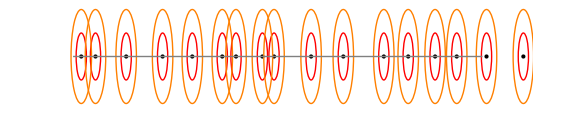

```mathematica
VisualizeField[Accumulate[Prepend[Subscript[r, data,0],0.4]],Subscript[V, pot],20]
```

```mathematica
(* without collision detection *)
Animate[VisualizeField[Subscript[q, data,0]+0.4+t Subscript[p, data,0],Subscript[V, pot],20],{t,0,10},AnimationRunning->False]
```

## Run simulation

```mathematica
(* example *)
NextCollision[Subscript[r, data,0],Subscript[p, data,0],Subscript[V, pot]]
```

{1/2,0.952159,0.180416,Core,6}

```mathematica
(* example *)
CollisionInfo[{Subscript[q, data,0],Subscript[p, data,0],0},Total[Subscript[r, data,0]],Subscript[V, pot]]
```

{0.180416,Core,6,{0.952159,-0.122305}}

```mathematica
(* example *)
UpdateField[{Subscript[q, data,0],Subscript[p, data,0],0},Total[Subscript[r, data,0]],Subscript[V, pot]]
Differences[First[%]]
```

{{0.0920776,0.743096,2.17425,4.20883,5.36353,6.95107,7.45107,8.79404,9.45463,11.26,12.813,14.9218,16.0807,17.3231,18.3831,19.9197},{0.510362,0.265417,-0.110275,1.3058,-0.330692,-0.60453,0.34763,-0.310875,0.204896,0.169026,0.0562263,0.780131,0.595775,0.203211,0.223302,0.670621},0.180416}

{0.651018,1.43115,2.03459,1.1547,1.58753,0.5,1.34297,0.660595,1.80539,1.55294,2.10884,1.15889,1.24245,1.05997,1.53658}

```mathematica
Subscript[f, seq]=FieldSequence[{Subscript[q, data,0],Subscript[p, data,0],0},Total[Subscript[r, data,0]],Subscript[V, pot],32];
Length[%]
```

33

```mathematica
(* example *)
Subscript[f, seq]⟦{1,2,-1}⟧
```

{{{0,0.69521,2.19414,3.97325,5.4232,6.88835,7.56013,8.85012,9.41766,11.2295,12.8028,14.781,15.9732,17.2865,18.3428,19.7987},{0.510362,0.265417,-0.110275,1.3058,-0.330692,0.34763,-0.60453,-0.310875,0.204896,0.169026,0.0562263,0.780131,0.595775,0.203211,0.223302,0.670621},0},{{0.0920776,0.743096,2.17425,4.20883,5.36353,6.95107,7.45107,8.79404,9.45463,11.26,12.813,14.9218,16.0807,17.3231,18.3831,19.9197},{0.510362,0.265417,-0.110275,1.3058,-0.330692,-0.60453,0.34763,-0.310875,0.204896,0.169026,0.0562263,0.780131,0.595775,0.203211,0.223302,0.670621},0.180416},{{0.891105,1.42799,2.5102,3.55097,4.55097,5.90904,7.89547,9.69618,10.958,12.289,14.1663,15.8475,16.9593,18.6181,19.9349,20.9889},{-0.60453,0.265417,-0.330692,-1.03443,0.670621,0.510362,-0.386142,0.169026,0.0562263,1.07119,1.89683,0.203211,0.223302,0.595775,0.780131,-0.110275},2.76087}}

```mathematica
Interpolation[{Last[#],First[#]}&/@Subscript[f, seq],InterpolationOrder->1]
Animate[VisualizeField[%[t],Subscript[V, pot],20],{t,0,1.9},AnimationRunning->False]
```

InterpolatingFunction[{{0., 2.76087}}, <>]

## Save currents to disk for comparison with C implementation

```mathematica
(* reference collisions *)
Subscript[coll, ref]=CollisionInfo[AdvanceField[#,0.0001],Total[Subscript[r, data,0]],Subscript[V, pot]]&/@Subscript[f, seq];
Length[%]
```

33

```mathematica
(* example *)
Subscript[coll, ref]⟦{1,2,-1}⟧
```

{{0.180416,Core,6,{0.952159,-0.122305}},{0.274949,PlatBounce,4,{1.63649,0.797873}},{2.81882,PlatBounce,3,{0.703739,-0.480346}}}

```mathematica
(* time slots for grouping collision events and corresponding currents *)
Subscript[t, slot]=2/5;
```

```mathematica
Subscript[J, list]=Table[1/Length[Subscript[r, data,0]] Total[Last/@Select[Subscript[coll, ref],((i-1)Subscript[t, slot]≤First[#]∧First[#]<i Subscript[t, slot])&]]/Subscript[t, slot],{i,5}]
```

{{0.404476,0.105558},{0.50099,0.1459},{0.763445,0.400454},{0.343773,0.214688},{0.712042,0.538921}}

```mathematica
(* save to disk for comparison *)
Export["current_test_Jref.dat",Flatten[Prepend[#,(*ignore Subscript[r, j] current*)0]&/@Subscript[J, list]],"Real64"];
```